## Bayesian Statistics, Assignment for Friday, Nov. 22

## Reading

I am having a rough time figuring out how to make Chapter 13 more digestible. So I don’t want you to start reading Chapter 13 yet. The problem is that Donovan and Mickey start into the rather advanced subject of Monte Carlo methods applied to Bayesian statistics without developing the ideas of Monte Carlo methods first. These ideas pre-date their application to Bayesian statistics by about 40 years. In fact, they were developed in the 1940s to deal with whether a chunk of enriched uranium would be a critical mass (e.g., whether or not it would support a runaway chain reaction).

The term Monte Carlo is a reference to gambling. You could call these “Las Vegas methods.” The idea is that you have modeled a system and that you want to look at a representative set of states in that model. For each state you are going to tabulate something. If the states are representative, it isn’t a big leap to hope that the tabulation is representative. The giant question that Monte Carlo methods solved is how you obtain a representative set of states for a complex system.

For the case of the atomic bomb, you want a representative set of paths that the neutrons released in each step of chain reaction follow. You can’t possible follow all the paths of all the neutrons, and even for a few dozen neutrons you can’t exhaustively examine all the different things each of those neutrons could do. So you are looking for a representative set of paths that the few dozen neutrons could follow and the reactions they could cause.

In preparation for learning about Monte Carlo methods as applied to Bayesian statistics, I’d like us all to luxuriate in an article about their invention. It is by the first author on the paper that revealed the Monte Carlo method to the world: “Equation of State Calculations by Fast Computing Machines,” Nicholas Metropolis, Arianna W. Rosenbluth, Marshall N. Rosenbluth, Augusta H. Teller, and Edward Teller, published in the Journal of Chemical Physics, June, 1953. Here is the article by Nicholas Metropolis, https://brianhill.github.io/bayesian-statistics/resources/TheBeginningOfTheMonteCarloMethod.pdf, and it is in your file folders. It is called “The Beginning of the Monte Carlo Method.”

Meanwhile I have a problem set for you that I hope will help solidify your understanding of Chapter 11.

## For Problem Set 14 — The Mug Breakage Problem — With a Gamma Function Prior

I was looking ahead to Chapter 11 when I wrote Problem 4 on Exam 2. You might remember that it was called “The Mug Breakage Problem — But with an Exponential Prior.” Why was the exponential prior problem preparation for gamma distribution priors!? Well, here is the gamma distribution prior:

P(a)=β^α/(Γ(α))a^(α-1)e^-βa

For the exam, I chose α=1, and β=2. Plugging that in, you get

P(a)=2^1/(Γ(1))a^(1-1)e^(-2a)=2/(Γ(1))a^0 e^(-2a)=2/(Γ(1))e^(-2a)

and it happens that Γ(1)=1 so this simplifies to

P(a)=2 e^(-2a)

which is exactly what I gave as the exponential prior on the exam problem.

## 1. Tabulating the Gamma Function

Now here is something confusing: this whole thing that we are looking at,

P(a)=β^α/(Γ(α))a^(α-1)e^-βa,

I have been calling  “the gamma function.”  It happens that the thing in the denominator that is needed to normalize this gamma function is also called “the gamma function.” What a pain. To disambiguate this annoying terminology collision I will try to be better and do what statisticians do which is to call the whole thing “the gamma distribution” and the denominator “the gamma function.”

Here is a graph of the gamma function:

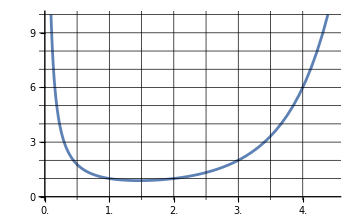

```mathematica
Plot[Gamma[x],{x, 0, 4.5},PlotRange->{{0.0,4.5},{0,10}}, GridLines->{Range[0,4,0.5],Range[0,10,1]}, GridLinesStyle->Directive[Black],Ticks->{Range[0.0,4.5,0.5],Range[0,10,1]}]
```

(a) Examining the graph on the previous page, please write down, what is

Γ(1)=

Γ(2)=

Γ(3)=

Γ(4)=

(b) If I told you that 

Γ(5)=24

Γ(6)=120

Γ(7)=720

could you make a guess as to what Γ(n+1) is?

Γ(n+1)=

For the formula you just guessed/discovered and checked against the above 7 cases, you can see why the gamma function is thought of as a generalization of the factorial function. The factorial function is only defined for integer values of n. Γ(n) has a value for all values of n, except at 0 and at any negative integer, where it blows up.

## 2. Exploring the Gamma Distribution

(a) Coming back to the gamma distribution

P(a)=β^α/(Γ(α))a^(α-1)e^-βa

Simplify this for the special case α=2 and β=3. Use what you found for Γ(2) in Problem 1 to finish the simplification.


P(a)=

I will have Mathematica plot the function you found:

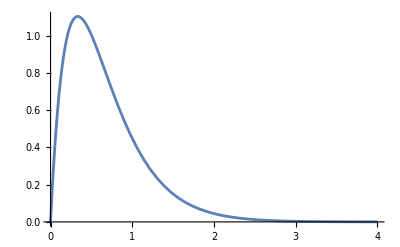

```mathematica
gamma[a_,α_,β_]:=β^α/Gamma[α] a^(α-1)Exp[-βa];
Plot[gamma[a,2,3],{a,0,4}]
```

(b) The junk out front of the function you found is just there to normalize the function to have total area 1 and it might be plausible that the function above indeed has area 1.If I had asked you to simplify the exact same function, except without the junk out front, you’d be simplifying  Q(a)=a^(α-1)e^-βa. Please simplify that for the same special case, α=2 and β=3:

 Q(a)=

(c) What is the area under the curve of Q(a)? (HINT: You know this because you know what junk was left off of the front).



(d) A bit of jargon is that since these are the same function of a, but with different factors out front (which do not involve a), we say these functions are proportional, and we write

Q(a)∝P(a).

The little fish that means proportionality looks an awful lot like an α, so be careful when reading and writing it. Here is a question for you:

Is (Q(a))/(∫_0^∞ Q(b)db) proportional to Q(a)?


(e) What is the area under the curve of the function (Q(a))/(∫_0^∞ Q(b)db)?

I hope this odd chain of questions helps you think a little more clearly about normalization factors and proportionality.

## 3. Some Likelihoods

The formula you need for likelihood in the case of Poisson distributions was on p. 59 of Young:
-Graphics-

We observe the kitchen for two weeks and see 4 mugs broken in one week and then 1 mug broken in the next.

(a) Write down the likelihood of having n=4 mugs broken in the first week.

(b) Repeat, but with n=1 mug for the second week.

(c) Take the product of what you got in (a) and (b).

P(data|a)=

## 4. The Posterior

In 2(a) you wrote down the prior, P(a). In 3(c) you wrote down the posterior, P(data|a).

By Bayes theorem, you know that the posterior is proportional to  P(data|a)P(a). The proportionality constant is something I often call “denominator” and it is

∫_0^∞ P(data|b)P(b)db

What Bayes theorem says is

P(a|data)=(P(data|a)P(a))/(∫_0^∞ P(data|b)P(b)db)


(a) Just ignore the denominator for a minute. It doesn’t depend on a, so it only changes the overall vertical scale of the function. Pretend for just a minute that it isn’t there, and if it weren’t then simplify:


P_(pretend version)(a|data)=P(data|a)P(a)=


Here’s another thing you can do. Just get rid of the 9  in the formula you just wrote by scratching it out, since we are throwing away proportionality factors.

(b) What gamma distribution is this proportional to? Once you have figured that out. Write down the whole gamma distribution:

α_posterior =


β_posterior=


P_(complete version)(a|data)=


(c) Remember how Jacob described it as “greedy” to use the formulas like 11.20 and 11.22 on p. 165 of Donovan and Mickey? Well, you have those formulas for the gamma distribution. Donovan and Mickey use n to mean the number of weeks of data, and they use ∑_(i=1)^n x_i to refer to the total number of mugs broken in those weeks. Can you double check that with n=2 and the total number of mugs broken = 5 that the α_posterior and β_posterior computed with their formulas agrees with what you got above? Greedy method:

α_posterior =

β_posterior=

(d) Hopefully the cross-check in (c) worked out. Finally, if you haven’t already, can you use what you learned about Γ(α) in Problem 1 to finish simplifying the real posterior with all the necessary normalization constants:

P(a|data)=

I hope by doing this specific example, you now see where the greedy formulas come from.